# Test NCS file reading

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

(last updated:  Sun 9 Feb 2014 22:32:57)

<<Set JLink` java stack size to 3072Mb>>

```mathematica
LoadJavaClass["nounou.NNJ"]
```

JavaClass[nounou.NNJ,<>]

```mathematica
console=ShowJavaConsole[]@toBack[]
```

```mathematica
nounou=JavaNew["nounou.DataReader"]
```

«JavaObject[nounou.DataReader]»

```mathematica
testFileHead = ParentDirectory[NotebookDirectory[]]<>"\\_testFiles\\Neuralynx"
```

V:\docs\bb\NounouM2\Testing\_testFiles\Neuralynx

## Load with ScalaFx window

```mathematica
nounou@load[]
```

Java::excptn: A Java exception occurred: "java.lang.IllegalStateException: Not on FX application thread; currentThread = J/Link reader\n\tat com.sun.javafx.tk.Toolkit.checkFxUserThread(Unknown Source)\n\tat com.sun.javafx.tk.quantum.QuantumToolkit.checkFxUserThread(Unknown Source)\n\tat javafx.scene.Scene.<init>(Unknown Source)\n\tat javafx.scene.Scene.<init>(Unknown Source)\n\tat javafx.stage.PopupWindow.<init>(Unknown Source)\n\tat javafx.stage.Popup.<init>(Unknown Source)\n\tat scalafx.stage.Popup$.$lessinit$greater$default$1(Popup.scala:41)\n\tat nounou.DataReader.load(DataReader.scala:37)".

## Load

```mathematica
nounou@reload[testFileHead<>"\\t130911\\Tet4a.ncs"]
```

```mathematica
nounou@data[]@segmentCount[]
```

3

```mathematica
(*Methods[nounou@data[]]*)
```

double absGain()
double absOffset()
String absUnit()
nounou.data.XDataChannel apply(int)
scala.collection.immutable.Vector array()
int channelCount()
scala.collection.immutable.Vector channelNames()
int currentSegment()
int currentSegment_$eq(int)
boolean equals(Object)
double framesPerTS()
long frameToTS(int, int)
Class getClass()
int hashCode()
boolean isCompatible(nounou.data.X)
boolean isValidChannel(int)
boolean isValidFrame(int)
boolean isValidFrame(int, int)
nounou.data.XDataChannelArray loadDataChannel(nounou.data.XDataChannel)
void notify()
void notifyAll()
void nounou$data$traits$XAbsoluteImmutable$_setter_$xBits_$eq(int)
int nounou$data$traits$XFrames$$_currentSegment()
void nounou$data$traits$XFrames$$_currentSegment_$eq(int)
scala.collection.immutable.Vector readFrameImpl(int, int)
scala.collection.immutable.Vector readFrameImpl(int, scala.collection.immutable.Vector, int)
scala.collection.immutable.Vector readFrame(int, int)
scala.collection.immutable.Vector readFrame(int, scala.collection.immutable.Vector, int)
double readPointAbs(int, int)
double readPointAbs(int, int, int)
int readPointImpl(int, int, int)
int readPoint(int, int)
int readPoint(int, int, int)
scala.collection.immutable.Vector readTraceAbs(int, nounou.data.Span)
scala.collection.immutable.Vector readTraceAbs(int, nounou.data.Span, int)
nounou.data.Span readTraceAbs$default$2()
scala.collection.immutable.Vector readTraceImpl(int, nounou.data.Span, int)
scala.collection.immutable.Vector readTrace(int)
scala.collection.immutable.Vector readTrace(int, nounou.data.Span)
scala.collection.immutable.Vector readTrace(int, nounou.data.Span, int)
double sampleInterval()
double sampleRate()
int segmentCount()
scala.collection.immutable.Vector segmentEndTSs()
scala.collection.immutable.Vector segmentLengths()
scala.collection.immutable.Vector segmentStartFrames()
scala.collection.immutable.Vector segmentStartTSs()
double toAbs(int)
scala.collection.immutable.Vector toAbs(scala.collection.immutable.Vector)
String toString()
double tsPerFrame()
scala.Tuple2 tsToFrame(long)
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException
int xBits()
double xBitsD()
nounou.data.XDataChannelArray $colon$colon$colon(nounou.data.X)
nounou.data.XData $colon$colon$colon(nounou.data.X)
nounou.data.X $colon$colon$colon(nounou.data.X)

### Try with scala methods (Vector is harder to read)

```mathematica
vect=nounou@data[]@readTrace[0, NNJ`Span[0,512*10,1], 0 ]
```

Java::argx: Method named "readTrace" defined in class "nounou.data.XDataChannelArray" was called with an incorrect number or type of arguments. The arguments, shown here in a list, were {0, 0 ;; 5120 ;; 1, 0}.

$Failed

```mathematica
vect@length[]
```

5121

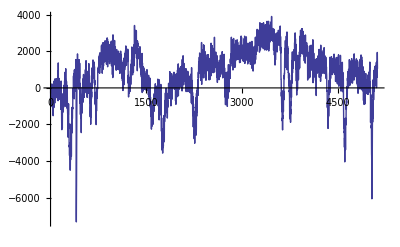

```mathematica
ListLinePlot[vect@apply[#]& /@ Range[0,512*10]/1024,PlotRange->All]
```

```mathematica
vect@apply[#]& /@ Range[0,9]/1024
```

{-888,-603,-107,1,-103,-102,-147,-366,-555,-520}

```mathematica
(*Methods[vect]*)
```

scala.collection.mutable.StringBuilder addString(scala.collection.mutable.StringBuilder)
scala.collection.mutable.StringBuilder addString(scala.collection.mutable.StringBuilder, String)
scala.collection.mutable.StringBuilder addString(scala.collection.mutable.StringBuilder, String, String, String)
Object aggregate(Object, scala.Function2, scala.Function2)
scala.Function1 andThen(scala.Function1)
scala.PartialFunction andThen(scala.Function1)
scala.Function1 andThen$mcDD$sp(scala.Function1)
scala.Function1 andThen$mcDF$sp(scala.Function1)
scala.Function1 andThen$mcDI$sp(scala.Function1)
scala.Function1 andThen$mcDJ$sp(scala.Function1)
scala.Function1 andThen$mcFD$sp(scala.Function1)
scala.Function1 andThen$mcFF$sp(scala.Function1)
scala.Function1 andThen$mcFI$sp(scala.Function1)
scala.Function1 andThen$mcFJ$sp(scala.Function1)
scala.Function1 andThen$mcID$sp(scala.Function1)
scala.Function1 andThen$mcIF$sp(scala.Function1)
scala.Function1 andThen$mcII$sp(scala.Function1)
scala.Function1 andThen$mcIJ$sp(scala.Function1)
scala.Function1 andThen$mcJD$sp(scala.Function1)
scala.Function1 andThen$mcJF$sp(scala.Function1)
scala.Function1 andThen$mcJI$sp(scala.Function1)
scala.Function1 andThen$mcJJ$sp(scala.Function1)
scala.Function1 andThen$mcVD$sp(scala.Function1)
scala.Function1 andThen$mcVF$sp(scala.Function1)
scala.Function1 andThen$mcVI$sp(scala.Function1)
scala.Function1 andThen$mcVJ$sp(scala.Function1)
scala.Function1 andThen$mcZD$sp(scala.Function1)
scala.Function1 andThen$mcZF$sp(scala.Function1)
scala.Function1 andThen$mcZI$sp(scala.Function1)
scala.Function1 andThen$mcZJ$sp(scala.Function1)
scala.collection.immutable.Vector appendBack(Object)
scala.collection.immutable.Vector appendFront(Object)
Object apply(int)
Object apply(Object)
Object applyOrElse(Object, scala.Function1)
double apply$mcDD$sp(double)
double apply$mcDF$sp(float)
double apply$mcDI$sp(int)
double apply$mcDJ$sp(long)
float apply$mcFD$sp(double)
float apply$mcFF$sp(float)
float apply$mcFI$sp(int)
float apply$mcFJ$sp(long)
int apply$mcID$sp(double)
int apply$mcIF$sp(float)
int apply$mcII$sp(int)
int apply$mcIJ$sp(long)
long apply$mcJD$sp(double)
long apply$mcJF$sp(float)
long apply$mcJI$sp(int)
long apply$mcJJ$sp(long)
void apply$mcVD$sp(double)
void apply$mcVF$sp(float)
void apply$mcVI$sp(int)
void apply$mcVJ$sp(long)
boolean apply$mcZD$sp(double)
boolean apply$mcZF$sp(float)
boolean apply$mcZI$sp(int)
boolean apply$mcZJ$sp(long)
static scala.collection.generic.CanBuildFrom canBuildFrom()
boolean canEqual(Object)
scala.Option collectFirst(scala.PartialFunction)
Object collect(scala.PartialFunction, scala.collection.generic.CanBuildFrom)
scala.collection.Iterator combinations(int)
scala.collection.generic.GenericCompanion companion()
scala.Function1 compose(scala.Function1)
scala.Function1 compose$mcDD$sp(scala.Function1)
scala.Function1 compose$mcDF$sp(scala.Function1)
scala.Function1 compose$mcDI$sp(scala.Function1)
scala.Function1 compose$mcDJ$sp(scala.Function1)
scala.Function1 compose$mcFD$sp(scala.Function1)
scala.Function1 compose$mcFF$sp(scala.Function1)
scala.Function1 compose$mcFI$sp(scala.Function1)
scala.Function1 compose$mcFJ$sp(scala.Function1)
scala.Function1 compose$mcID$sp(scala.Function1)
scala.Function1 compose$mcIF$sp(scala.Function1)
scala.Function1 compose$mcII$sp(scala.Function1)
scala.Function1 compose$mcIJ$sp(scala.Function1)
scala.Function1 compose$mcJD$sp(scala.Function1)
scala.Function1 compose$mcJF$sp(scala.Function1)
scala.Function1 compose$mcJI$sp(scala.Function1)
scala.Function1 compose$mcJJ$sp(scala.Function1)
scala.Function1 compose$mcVD$sp(scala.Function1)
scala.Function1 compose$mcVF$sp(scala.Function1)
scala.Function1 compose$mcVI$sp(scala.Function1)
scala.Function1 compose$mcVJ$sp(scala.Function1)
scala.Function1 compose$mcZD$sp(scala.Function1)
scala.Function1 compose$mcZF$sp(scala.Function1)
scala.Function1 compose$mcZI$sp(scala.Function1)
scala.Function1 compose$mcZJ$sp(scala.Function1)
static scala.collection.GenTraversable concat(scala.collection.Seq)
boolean contains(Object)
boolean containsSlice(scala.collection.GenSeq)
Object[] copyOf(Object[])
Object[] copyRange(Object[], int, int)
void copyToArray(Object)
void copyToArray(Object, int)
void copyToArray(Object, int, int)
void copyToBuffer(scala.collection.mutable.Buffer)
boolean corresponds(scala.collection.GenSeq, scala.Function2)
int count(scala.Function1)
void debug()
int depth()
void depth_$eq(int)
Object diff(scala.collection.GenSeq)
boolean dirty()
void dirty_$eq(boolean)
Object[] display0()
void display0_$eq(Object[])
Object[] display1()
void display1_$eq(Object[])
Object[] display2()
void display2_$eq(Object[])
Object[] display3()
void display3_$eq(Object[])
Object[] display4()
void display4_$eq(Object[])
Object[] display5()
void display5_$eq(Object[])
Object distinct()
Object drop(int)
scala.collection.immutable.Vector drop(int)
Object dropRight(int)
scala.collection.immutable.Vector dropRight(int)
Object dropWhile(scala.Function1)
static scala.collection.GenTraversable empty()
static scala.collection.immutable.Vector empty()
int endIndex()
boolean endsWith(scala.collection.GenSeq)
boolean equals(Object)
boolean exists(scala.Function1)
static scala.collection.GenTraversable fill(int, int, int, int, int, scala.Function0)
static scala.collection.GenTraversable fill(int, int, int, int, scala.Function0)
static scala.collection.GenTraversable fill(int, int, int, scala.Function0)
static scala.collection.GenTraversable fill(int, int, scala.Function0)
static scala.collection.GenTraversable fill(int, scala.Function0)
Object filterNot(scala.Function1)
Object filter(scala.Function1)
scala.Option find(scala.Function1)
Object flatMap(scala.Function1, scala.collection.generic.CanBuildFrom)
scala.collection.GenTraversable flatten(scala.Function1)
Object foldLeft(Object, scala.Function2)
Object fold(Object, scala.Function2)
Object foldRight(Object, scala.Function2)
boolean forall(scala.Function1)
void foreach(scala.Function1)
scala.collection.mutable.Builder genericBuilder()
Class getClass()
Object getElem(int, int)
void gotoFreshPosWritable0(int, int, int)
void gotoFreshPosWritable1(int, int, int)
void gotoNextBlockStart(int, int)
void gotoNextBlockStartWritable(int, int)
void gotoPos(int, int)
void gotoPosWritable0(int, int)
void gotoPosWritable1(int, int, int)
scala.collection.GenMap groupBy(scala.Function1)
scala.collection.immutable.Map groupBy(scala.Function1)
scala.collection.Iterator grouped(int)
boolean hasDefiniteSize()
int hashCode()
Object head()
scala.Option headOption()
int indexOf(Object)
int indexOf(Object, int)
int indexOfSlice(scala.collection.GenSeq)
int indexOfSlice(scala.collection.GenSeq, int)
int indexWhere(scala.Function1)
int indexWhere(scala.Function1, int)
scala.collection.immutable.Range indices()
Object init()
scala.collection.immutable.Vector init()
void initFrom(scala.collection.immutable.VectorPointer)
void initFrom(scala.collection.immutable.VectorPointer, int)
void initIterator(scala.collection.immutable.VectorIterator)
scala.collection.Iterator inits()
Object intersect(scala.collection.GenSeq)
boolean isDefinedAt(int)
boolean isDefinedAt(Object)
boolean isEmpty()
boolean isTraversableAgain()
static scala.collection.GenTraversable iterate(Object, int, scala.Function1)
scala.collection.immutable.VectorIterator iterator()
scala.collection.Iterator iterator()
Object last()
int lastIndexOf(Object)
int lastIndexOf(Object, int)
int lastIndexOfSlice(scala.collection.GenSeq)
int lastIndexOfSlice(scala.collection.GenSeq, int)
int lastIndexWhere(scala.Function1)
int lastIndexWhere(scala.Function1, int)
scala.Option lastOption()
int length()
int lengthCompare(int)
scala.Function1 lift()
Object map(scala.Function1, scala.collection.generic.CanBuildFrom)
Object maxBy(scala.Function1, scala.math.Ordering)
Object max(scala.math.Ordering)
Object minBy(scala.Function1, scala.math.Ordering)
Object min(scala.math.Ordering)
String mkString()
String mkString(String)
String mkString(String, String, String)
scala.collection.mutable.Builder newBuilder()
boolean nonEmpty()
void notify()
void notifyAll()
Object[] nullSlotAndCopy(Object[], int)
scala.PartialFunction orElse(scala.PartialFunction)
Object padTo(int, Object, scala.collection.generic.CanBuildFrom)
scala.collection.parallel.immutable.ParVector par()
scala.collection.Parallel par()
scala.collection.parallel.Combiner parCombiner()
scala.Tuple2 partition(scala.Function1)
Object patch(int, scala.collection.GenSeq, int, scala.collection.generic.CanBuildFrom)
scala.collection.Iterator permutations()
int prefixLength(scala.Function1)
Object product(scala.math.Numeric)
static scala.collection.GenTraversable range(Object, Object, Object, scala.math.Integral)
static scala.collection.GenTraversable range(Object, Object, scala.math.Integral)
scala.Option reduceLeftOption(scala.Function2)
Object reduceLeft(scala.Function2)
scala.Option reduceOption(scala.Function2)
scala.Option reduceRightOption(scala.Function2)
Object reduceRight(scala.Function2)
Object reduce(scala.Function2)
Object repr()
static scala.collection.generic.GenTraversableFactory$GenericCanBuildFrom ReusableCBF()
Object reverse()
scala.collection.immutable.List reversed()
scala.collection.Iterator reverseIterator()
Object reverseMap(scala.Function1, scala.collection.generic.CanBuildFrom)
scala.Function1 runWith(scala.Function1)
boolean sameElements(scala.collection.GenIterable)
Object scanLeft(Object, scala.Function2, scala.collection.generic.CanBuildFrom)
Object scan(Object, scala.Function2, scala.collection.generic.CanBuildFrom)
Object scanRight(Object, scala.Function2, scala.collection.generic.CanBuildFrom)
int segmentLength(scala.Function1, int)
scala.collection.immutable.IndexedSeq seq()
scala.collection.immutable.Iterable seq()
scala.collection.immutable.Seq seq()
scala.collection.immutable.Traversable seq()
scala.collection.IndexedSeq seq()
scala.collection.Iterable seq()
scala.collection.Seq seq()
scala.collection.TraversableOnce seq()
scala.collection.Traversable seq()
int size()
Object slice(int, int)
scala.collection.immutable.Vector slice(int, int)
Object sliceWithKnownBound(int, int)
Object sliceWithKnownDelta(int, int, int)
scala.collection.Iterator sliding(int)
scala.collection.Iterator sliding(int, int)
Object sortBy(scala.Function1, scala.math.Ordering)
Object sorted(scala.math.Ordering)
Object sortWith(scala.Function2)
scala.Tuple2 span(scala.Function1)
scala.Tuple2 splitAt(int)
void stabilize(int)
int startIndex()
boolean startsWith(scala.collection.GenSeq)
boolean startsWith(scala.collection.GenSeq, int)
String stringPrefix()
Object sum(scala.math.Numeric)
static scala.collection.GenTraversable tabulate(int, int, int, int, int, scala.Function5)
static scala.collection.GenTraversable tabulate(int, int, int, int, scala.Function4)
static scala.collection.GenTraversable tabulate(int, int, int, scala.Function3)
static scala.collection.GenTraversable tabulate(int, int, scala.Function2)
static scala.collection.GenTraversable tabulate(int, scala.Function1)
Object tail()
scala.collection.immutable.Vector tail()
scala.collection.Iterator tails()
Object take(int)
scala.collection.immutable.Vector take(int)
Object takeRight(int)
scala.collection.immutable.Vector takeRight(int)
Object takeWhile(scala.Function1)
scala.collection.IndexedSeq thisCollection()
scala.collection.Iterable thisCollection()
scala.collection.Seq thisCollection()
scala.collection.Traversable thisCollection()
Object toArray(scala.reflect.ClassTag)
scala.collection.mutable.Buffer toBuffer()
scala.collection.IndexedSeq toCollection(Object)
scala.collection.Iterable toCollection(Object)
scala.collection.Seq toCollection(Object)
scala.collection.Traversable toCollection(Object)
scala.collection.immutable.IndexedSeq toIndexedSeq()
scala.collection.GenIterable toIterable()
scala.collection.Iterable toIterable()
scala.collection.Iterator toIterator()
scala.collection.immutable.List toList()
scala.collection.GenMap toMap(scala.Predef$$less$colon$less)
scala.collection.immutable.Map toMap(scala.Predef$$less$colon$less)
Object to(scala.collection.generic.CanBuildFrom)
scala.collection.GenSeq toSeq()
scala.collection.immutable.Seq toSeq()
scala.collection.Seq toSeq()
scala.collection.GenSet toSet()
scala.collection.immutable.Set toSet()
scala.collection.immutable.Stream toStream()
String toString()
scala.collection.GenTraversable toTraversable()
scala.collection.Traversable toTraversable()
scala.collection.immutable.Vector toVector()
scala.collection.GenTraversable transpose(scala.Function1)
static scala.Some unapplySeq(scala.collection.Seq)
Object union(scala.collection.GenSeq, scala.collection.generic.CanBuildFrom)
scala.Tuple3 unzip3(scala.Function1)
scala.Tuple2 unzip(scala.Function1)
scala.collection.immutable.Vector updateAt(int, Object)
Object updated(int, Object, scala.collection.generic.CanBuildFrom)
scala.collection.IterableView view()
scala.collection.SeqView view()
scala.collection.TraversableView view()
scala.collection.IterableView view(int, int)
scala.collection.SeqView view(int, int)
scala.collection.TraversableView view(int, int)
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException
scala.collection.generic.FilterMonadic withFilter(scala.Function1)
Object zipAll(scala.collection.GenIterable, Object, Object, scala.collection.generic.CanBuildFrom)
Object zip(scala.collection.GenIterable, scala.collection.generic.CanBuildFrom)
Object zipWithIndex(scala.collection.generic.CanBuildFrom)
Object $colon$bslash(Object, scala.Function2)
Object $colon$plus(Object, scala.collection.generic.CanBuildFrom)
Object $div$colon(Object, scala.Function2)
Object $div$colon$bslash(Object, scala.Function2)
Object $plus$colon(Object, scala.collection.generic.CanBuildFrom)
Object $plus$plus(scala.collection.GenTraversableOnce, scala.collection.generic.CanBuildFrom)
Object $plus$plus$colon(scala.collection.TraversableOnce, scala.collection.generic.CanBuildFrom)
Object $plus$plus$colon(scala.collection.Traversable, scala.collection.generic.CanBuildFrom)

### Read by point

```mathematica
tempPoints=nounou@data[]@readPointAbs[0, #, 0 ]& /@ Range[0,512*10];
```

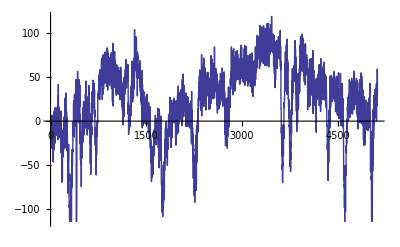

```mathematica
ListLinePlot[tempPoints]
```

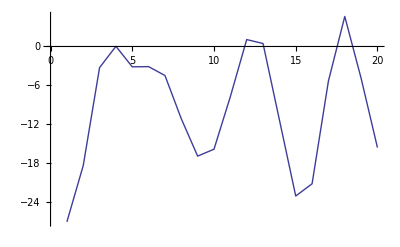

```mathematica
ListLinePlot[tempPoints[[1;;20]]]
```

### Try with java-oriented methods

```mathematica
tempTrace=nounou@dataReadTraceAbs[0, NNJ`Span[0,512*10,1], 0 ];
```

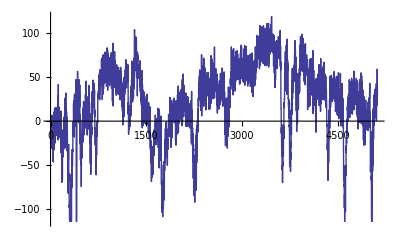

```mathematica
ListLinePlot[tempTrace]
```

```mathematica
tempTrace[[1 ;; 12]]
```

{-27.1004,-18.4027,-3.26548,0.0305185,-3.14341,-3.11289,-4.48622,-11.1698,-16.9378,-15.8696,-7.7517,1.06815}

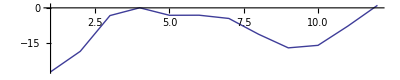

```mathematica
ListLinePlot[tempTrace[[1 ;; 12]],AspectRatio->1/5,PlotRange->All]
```

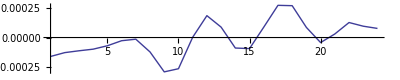

```mathematica
ListLinePlot[tempTrace[[501 ;; 524]],AspectRatio->1/5,PlotRange->All]
```

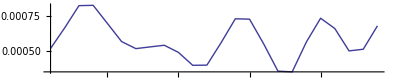

```mathematica
ListLinePlot[tempTrace[[512+501 ;; 512+524]],AspectRatio->1/5,PlotRange->All]
```

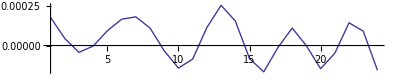

```mathematica
ListLinePlot[tempTrace[[512*2+501 ;; 512*2+524]],AspectRatio->1/5,PlotRange->All]
```

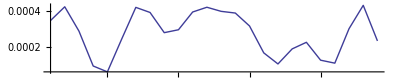

```mathematica
ListLinePlot[tempTrace[[512*3+501 ;; 512*3+524]],AspectRatio->1/5,PlotRange->All]
```

### Read segment info

```mathematica
Length[nounou@dataReadTraceAbs[0, NNJ`SpanAll, 0 ]]
```

3339265

```mathematica
segStarts=nounou@data[]@segmentStartFrames[]@apply[#]& /@Range[0,3]
```

Java::excptn: A Java exception occurred: "java.lang.IndexOutOfBoundsException: 3\n\tat scala.collection.immutable.Vector.checkRangeConvert(Vector.scala:137)\n\tat scala.collection.immutable.Vector.apply(Vector.scala:127)".

{0,3339264,3462656,$Failed}

```mathematica
segStarts=nounou@data[]@segmentStartFrames[]@toString[]
```

Vector(0, 3339264, 3462656)

```mathematica
nounou@data[]@segmentLengths[]@toString[]
```

Vector(3339264, 123392, 6754816)

```mathematica
3339265/512.
```

6522.

## Load Timing

```mathematica
Timing[Length[nounou@dataReadTrace[0, NNJ`Span[0,512*6521,1], 0 ]];]
```

{0.,Null}

```mathematica
timings=Table[
{n,
tempTime=AbsoluteTime[];
Length[nounou@dataReadTrace[0, NNJ`Span[0,512*n,1], 0 ]];
AbsoluteTime[]-tempTime},
{n,1,6500,500}
]
```

{{1,0.002},{501,0.5280303},{1001,1.949111},{1501,4.3692499},{2001,7.7924457},{2501,12.142695},{3001,17.624008},{3501,24.106379},{4001,31.497802},{4501,39.1152372},{5001,48.3257641},{5501,59.530405},{6001,70.1920147}}

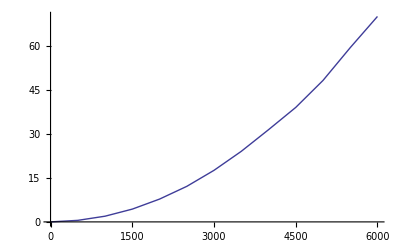

```mathematica
ListLinePlot[timings]
```